```mathematica
x1=4.59;
x2=1.34;
x3=1;
a0=1;
a1=1.15;
a2=0.38;
a3=20.3597;
A=Table[0,{x,4},{y,4}];
A[[1,1]]=-2*a0*x3;
A[[1,2]]=0;
A[[1,3]]=a0*x1+a1*x3;
A[[1,4]]=a0*x2-a2*x3;
A[[2,1]]=0;
A[[2,2]]=-2*a0*x3;
A[[2,3]]=a0*x2+a2*x3;
A[[2,4]]=-a0*x1+a1*x3;
A[[3,1]]=a0*x1+a1*x3;
A[[3,2]]=a0*x2+a2*x3;
A[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A[[3,4]]=a2*x1-a1*x2;
A[[4,1]]=a0*x2-a2*x3;
A[[4,2]]=-a0*x1+a1*x3;
A[[4,3]]=a2*x1-a1*x2;
A[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A
```

{{-2,0,5.74,0.96},{0,-2,1.72,-3.44},{5.74,1.72,-7.0397,0.2032},{0.96,-3.44,0.2032,4.5357}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

-2

9.18

2.68

2.3

0.76

0.4064

-5.7877

-1.252

```mathematica
x1=1.24;
x2=0.1;
x3=1;
a0=1;
a1=-2.20;
a2=-0.10;
a3=-3.3177;
B=Table[0,{x,4},{y,4}];
B[[1,1]]=-2*a0*x3;
B[[1,2]]=0;
B[[1,3]]=a0*x1+a1*x3;
B[[1,4]]=a0*x2-a2*x3;
B[[2,1]]=0;
B[[2,2]]=-2*a0*x3;
B[[2,3]]=a0*x2+a2*x3;
B[[2,4]]=-a0*x1+a1*x3;
B[[3,1]]=a0*x1+a1*x3;
B[[3,2]]=a0*x2+a2*x3;
B[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
B[[3,4]]=a2*x1-a1*x2;
B[[4,1]]=a0*x2-a2*x3;
B[[4,2]]=-a0*x1+a1*x3;
B[[4,3]]=a2*x1-a1*x2;
B[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
B
```

{{-2,0,-0.96,0.2},{0,-2,0.,-3.44},{-0.96,0.,0.30535,0.096},{0.2,-3.44,0.096,-5.17065}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

-2

2.48

0.2

-4.4

-0.2

0.192

2.738

-2.43265

```mathematica
myplot=ContourPlot3D[{A[[1, 1]]*x^2 + (A[[1, 2]] + A[[2, 1]])*x*y + (A[[1, 3]] + A[[3, 1]])*x*z + (A[[1, 4]] + A[[4, 1]])*x + A[[2, 2]]*y^2 + (A[[2, 3]] + A[[3, 2]])*y*z + (A[[2, 4]] + A[[4, 2]])*y + A[[3, 3]]*z^2 + (A[[3, 4]] + A[[4, 3]])*z + A[[4, 4]] == 0, B[[1, 1]]*x^2 + (B[[1, 2]] + B[[2, 1]])*x*y + (B[[1, 3]] + B[[3, 1]])*x*z + (B[[1, 4]] + B[[4, 1]])*x + B[[2, 2]]*y^2 + (B[[2, 3]] + B[[3, 2]])*y*z + (B[[2, 4]] + B[[4, 2]])*y + B[[3, 3]]*z^2 + (B[[3, 4]] + B[[4, 3]])*z + B[[4, 4]] == 0}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, PerformanceGoal -> "Quality", MeshStyle -> Gray, Mesh -> 2, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}, MaxRecursion -> 15, PlotPoints -> 50, PlotRange -> Automatic, ContourStyle -> {{Orange, Opacity[0.4]}, {Magenta,Opacity[0.4]}}];
Show[myplot]
```

-Graphics3D-

```mathematica
eigenvalues=Eigenvalues[A];
eigenvectors=Eigenvectors[A];
transformatrix=Transpose[{eigenvectors[[2]],eigenvectors[[4]],eigenvectors[[1]], eigenvectors[[3]]}];
```

```mathematica
afterA=Transpose[transformatrix].A.transformatrix;
MatrixForm[afterA]
```

(6.11097 | -8.32667×10^-16 | 7.07767×10^-16 | 4.44089×10^-16
-7.59809×10^-16 | 1.98004 | -2.16992×10^-15 | -5.26489×10^-16
7.49401×10^-16 | -1.62782×10^-15 | -11.0233 | 8.46545×10^-16
-2.22045×10^-16 | -3.85109×10^-16 | 8.1532×10^-16 | -3.57171)

```mathematica
afterB=Transpose[transformatrix].B.transformatrix;
MatrixForm[afterB]
```

(-2.18955 | -0.625026 | -0.459793 | -3.42206
-0.625026 | -2.12728 | -0.710304 | -0.0673219
-0.459793 | -0.710304 | 0.427576 | -0.515306
-3.42206 | -0.0673219 | -0.515306 | -4.97605)

```mathematica
Clear[V];Clear[u];Clear[v];
V={(u+afterA[[1,1]]*v)/afterA[[1,1]], (u*v-afterA[[2,2]])/afterA[[2,2]], (u-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
goalformula=Collect[Expand[V.afterB.V], {u^2, u}]
```

-4.78559-4.33219 v-1.26783 v^2+u (-0.549735-1.43182 v-2.38219 v^2)+u^2 (-0.0706191-0.65909 v-1.27178 v^2)

```mathematica
delta=Expand[(-0.5497352512103473-1.4318190764043104 v-2.3821935803136935 v^2)^2-4*(-0.07061908945122576-0.6590900396041321 v-1.2717804537651367 v^2)*(-4.785594228656201-4.33219342064068 v-1.2678256786728286 v^2)];
```

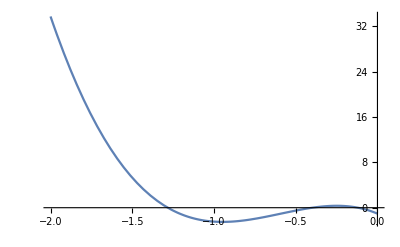

```mathematica
Plot[delta, {v,-2, 0}]
```

```mathematica
Solve[delta==0, v]
```

{{v→-22.1549},{v→-1.28262},{v→-0.398072},{v→-0.119769}}

```mathematica
u1=(-(-0.5497352512103473-1.4318190764043104 v-2.3821935803136935 v^2)+Sqrt[delta])/(2*(-0.07061908945122576-0.6590900396041321 v-1.2717804537651367 v^2));
u2=(-(-0.5497352512103473-1.4318190764043104 v-2.3821935803136935 v^2)-Sqrt[delta])/(2*(-0.07061908945122576-0.6590900396041321 v-1.2717804537651367 v^2));
```

```mathematica
afterP1={(u1+afterA[[1,1]]*v)/afterA[[1,1]], (u1*v-afterA[[2,2]])/afterA[[2,2]], (u1-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u1*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
afterP2={(u2+afterA[[1,1]]*v)/afterA[[1,1]], (u2*v-afterA[[2,2]])/afterA[[2,2]], (u2-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u2*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
P1=transformatrix.afterP1;
P2=transformatrix.afterP2;
```

```mathematica
Branch11=Graphics3D[{PointSize[0.015],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,-22.15, -1.29, 0.005}]]}, Axes -> True, AxesLabel -> {X, Y, Z},Boxed -> False];
Branch12=Graphics3D[{PointSize[0.015],Black,Point[Table[{P2[[1]]/P2[[4]],P2[[2]]/P2[[4]],P2[[3]]/P2[[4]]},{v,-22.15 ,-1.29, 0.005}]]}];
Branch21=Graphics3D[{PointSize[0.015],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,-0.3980, -0.1198, 0.0001}]]}];
Branch22=Graphics3D[{PointSize[0.015],Black,Point[Table[{P2[[1]]/P2[[4]],P2[[2]]/P2[[4]],P2[[3]]/P2[[4]]},{v,-0.3980,-0.1198, 0.0005}]]}];
Show[Branch11,Branch12,Branch21,Branch22,myplot]
```

-Graphics3D-